# COVID-19 Data Acquisition South Korea Provinces

## 장유성 | Yu-Sung Chang CTO, Digital Innovation Group SSG.COM

## Config

```mathematica
$baseDirectory=If[$Notebooks, NotebookDirectory[], Directory[]<>"/"];
```

```mathematica
$configDirectory=$baseDirectory<>"../config/";
```

```mathematica
$dataDirectory=$baseDirectory<>"../data/";
```

```mathematica
$cacheDirectory=$baseDirectory<>"../data/cache/";
```

```mathematica
$outputDirectory=$baseDirectory<>"../src/output/";
```

```mathematica
allCaches=Import[#,"String"]&/@FileNames[$cacheDirectory<>"*.html"];
```

```mathematica
$provinces={"서울","부산","대구","인천","광주","대전","울산","세종","경기","강원","충북","충남","전북","전남","경북","경남","제주"};
```

## Samples

### Old Horizontal

2020-02-21

### Vertical

2020 -02-24

### Horizontal

## Extraction

```mathematica
MapIndexed[#2->ImportString[#1,"Title"]&,allCaches]
```

{{1}→코로나바이러스감염증-19 국내 발생 현황(2월 12일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{2}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{3}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{4}→코로나바이러스감염증-19 국내 발생 현황(2월 13일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{5}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{6}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 09시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{7}→코로나바이러스감염증-19 국내 발생 현황(2월 14일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{8}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{9}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 09시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{10}→코로나바이러스감염증-19 국내 발생 현황(2월 15일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{11}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{12}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{13}→코로나바이러스감염증-19 국내 발생 현황(2월 16일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{14}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{15}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{16}→코로나바이러스감염증-19 국내 발생 현황(2월 17일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{17}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{18}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{19}→코로나바이러스감염증-19 국내 발생 현황(2월 18일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{20}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{21}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{22}→코로나바이러스감염증-19 국내 발생 현황(2월 19일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{23}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{24}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{25}→코로나바이러스감염증-19 국내 발생 현황(2월 20일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{26}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{27}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{28}→코로나바이러스감염증-19 국내 발생 현황(2월 21일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{29}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{30}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{31}→코로나바이러스감염증-19 국내 발생 현황(2월 22일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{32}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{33}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{34}→코로나바이러스감염증-19 국내 발생 현황(2월 23일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{35}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{36}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{37}→코로나바이러스감염증-19 국내 발생 현황(2월 24일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{38}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{39}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{40}→코로나바이러스감염증-19 국내 발생 현황(2월 25일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{41}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{42}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{43}→코로나바이러스감염증-19 국내 발생 현황(2월 26일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{44}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{45}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{46}→코로나바이러스감염증-19 국내 발생 현황(2월 27일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{47}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{48}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 9시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{49}→코로나바이러스감염증-19 국내 발생 현황(2월 28일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{50}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{51}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 09시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{52}→코로나바이러스감염증-19 국내 발생 현황(2월 29일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{53}→코로나바이러스감염증-19 국내 발생 현황(2월 29일, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{54}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 09시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{55}→코로나바이러스감염증-19 국내 발생 현황(3월 1일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{56}→코로나바이러스감염증-19 국내 발생 현황(일일집계통계, 16시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{57}→코로나바이러스감염증-19 국내 발생 현황(3월 2일, 0시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{58}→코로나바이러스감염증-19 국내 발생 현황(3월 2일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{59}→코로나바이러스감염증-19 국내 발생 현황(3월 3일, 0시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{60}→코로나바이러스감염증-19 국내 발생 현황(3월 3일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{61}→코로나바이러스감염증-19 국내 발생 현황(3월 4일, 0시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{62}→코로나바이러스감염증-19 국내 발생 현황(3월 4일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{63}→코로나바이러스감염증-19 국내 발생 현황(3월 5일, 0시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{64}→코로나바이러스감염증-19 국내 발생 현황(3월 5일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{65}→코로나바이러스감염증-19 국내 발생 현황(3월 6일, 0시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{66}→코로나바이러스감염증-19 국내 발생 현황(3월 6일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{67}→코로나바이러스감염증-19 국내 발생 현황(3월 7일, 0시 기준) | 보도자료 | 알림·자료 : 질병관리본부,{68}→코로나바이러스감염증-19 국내 발생 현황(3월 7일, 정례브리핑) | 보도자료 | 알림·자료 : 질병관리본부,{69}→코로나바이러스감염증-19 국내 발생 현황(3월 8일, 0시 기준) | 보도자료 | 알림·자료 : 질병관리본부}

```mathematica
Clear[filter];
filter[cache_]:=With[{title=ImportString[cache,"Title"]},
If[Length@StringCases[title,"정례브리핑"]>0,
PrintTemporary[title];
Module[{date,do,data,pos,table,header,r,c,col,values,assoc},
date=First@StringCases[title,(x:DigitCharacter..)~~"월"~~(" "...)~~(y:DigitCharacter..)~~"일":>x<>"-"<>y]; (* 날짜 *)
do=DateObject@date;
(* 테이블 *)
data=ImportString[cache,"Data"];
pos=Position[data,x_/;ContainsAll[{"합계","구분"}~Join~$provinces,StringReplace[x," ":>""]]]; (* Check horizontal table header *)
If[pos=={},(* Try vertical *)
pos=Position[data,x_/;ContainsAll[{"지역","확진환자","비고","주요기타유행"},StringReplace[x," ":>""]]];
If[pos=={},
None,
(* Process vertical table *)
pos=First@pos;
table=Part[data,Sequence@@Most@pos];
header=StringReplace[First@#," ":>""]&/@table;
values=ToExpression[StringReplace[Part[#,2],{" ":>"",",":>""}]]&/@table;(* Assuming that 2nd column is the values *)
assoc=AssociationThread[$provinces->Lookup[AssociationThread[header->values],$provinces]];
{do,Sequence@@Values[assoc]}
],
(* Process horizontal table *)
pos=First@pos;
table=Part[data,Sequence@@Most@pos];
header=StringReplace[Part[data,Sequence@@pos]," ":>""];
c=First@First@Position[header,"합계"];
col=Quiet[ToExpression/@((StringReplace[Part[#,c],",":>""])&/@table)];
r=First@First@Position[col,First@Max[col]];
values=ToExpression[StringReplace[#,",":>""]]&/@table[[r]];
assoc=AssociationThread[$provinces->Lookup[AssociationThread[header->values],$provinces]];
{do,Sequence@@Values[assoc]}
]
],
None]
];
```

```mathematica
rule=DeleteCases[Quiet[filter/@allCaches],None]
```

{{Fri 21 Feb 2020 00:00:00GMT+9.,4,Missing[KeyAbsent,부산],45,Missing[KeyAbsent,인천],1,Missing[KeyAbsent,대전],Missing[KeyAbsent,울산],Missing[KeyAbsent,세종],1,Missing[KeyAbsent,강원],1,1,1,Missing[KeyAbsent,전남],17,2,1},{Mon 24 Feb 2020 00:00:00GMT+9.,30,17,443,2,9,3,1,1,35,6,3,1,3,1,186,20,2},{Tue 25 Feb 2020 00:00:00GMT+9.,36,38,499,2,9,3,2,1,40,6,3,1,3,2,225,21,2},{Wed 26 Feb 2020 00:00:00GMT+9.,45,50,677,3,9,3,3,1,43,6,5,2,3,1,268,25,2},{Thu 27 Feb 2020 00:00:00GMT+9.,55,58,1017,3,9,8,6,1,55,6,7,7,3,1,321,36,2},{Fri 28 Feb 2020 00:00:00GMT+9.,62,63,1314,4,9,13,11,1,66,6,9,16,5,1,394,46,2},{Sat 29 Feb 2020 00:00:00GMT+9.,74,77,2055,6,9,14,17,1,76,7,10,48,5,2,469,59,2},{Sun 1 Mar 2020 00:00:00GMT+9.,82,81,2569,6,9,13,17,1,84,7,11,60,5,3,514,62,2},{Mon 2 Mar 2020 00:00:00GMT+9.,91,88,3081,7,9,14,20,1,92,19,11,78,6,5,624,64,2},{Tue 3 Mar 2020 00:00:00GMT+9.,98,90,3601,7,11,14,20,1,94,20,11,81,7,5,685,64,3},{Wed 4 Mar 2020 00:00:00GMT+9.,99,93,4006,9,13,15,23,1,101,21,11,82,7,5,774,65,3},{Thu 5 Mar 2020 00:00:00GMT+9.,103,92,4327,9,14,16,23,1,110,23,12,86,7,4,861,74,4},{Fri 6 Mar 2020 00:00:00GMT+9.,105,95,4694,9,13,18,23,1,120,25,15,90,7,4,984,77,4},{Sat 7 Mar 2020 00:00:00GMT+9.,108,96,5084,9,13,18,23,2,130,26,20,92,7,4,1049,82,4}}

```mathematica
data=ReplaceAll[rule,_Missing:>0]
```

{{Fri 21 Feb 2020 00:00:00GMT+9.,4,0,45,0,1,0,0,0,1,0,1,1,1,0,17,2,1},{Mon 24 Feb 2020 00:00:00GMT+9.,30,17,443,2,9,3,1,1,35,6,3,1,3,1,186,20,2},{Tue 25 Feb 2020 00:00:00GMT+9.,36,38,499,2,9,3,2,1,40,6,3,1,3,2,225,21,2},{Wed 26 Feb 2020 00:00:00GMT+9.,45,50,677,3,9,3,3,1,43,6,5,2,3,1,268,25,2},{Thu 27 Feb 2020 00:00:00GMT+9.,55,58,1017,3,9,8,6,1,55,6,7,7,3,1,321,36,2},{Fri 28 Feb 2020 00:00:00GMT+9.,62,63,1314,4,9,13,11,1,66,6,9,16,5,1,394,46,2},{Sat 29 Feb 2020 00:00:00GMT+9.,74,77,2055,6,9,14,17,1,76,7,10,48,5,2,469,59,2},{Sun 1 Mar 2020 00:00:00GMT+9.,82,81,2569,6,9,13,17,1,84,7,11,60,5,3,514,62,2},{Mon 2 Mar 2020 00:00:00GMT+9.,91,88,3081,7,9,14,20,1,92,19,11,78,6,5,624,64,2},{Tue 3 Mar 2020 00:00:00GMT+9.,98,90,3601,7,11,14,20,1,94,20,11,81,7,5,685,64,3},{Wed 4 Mar 2020 00:00:00GMT+9.,99,93,4006,9,13,15,23,1,101,21,11,82,7,5,774,65,3},{Thu 5 Mar 2020 00:00:00GMT+9.,103,92,4327,9,14,16,23,1,110,23,12,86,7,4,861,74,4},{Fri 6 Mar 2020 00:00:00GMT+9.,105,95,4694,9,13,18,23,1,120,25,15,90,7,4,984,77,4},{Sat 7 Mar 2020 00:00:00GMT+9.,108,96,5084,9,13,18,23,2,130,26,20,92,7,4,1049,82,4}}

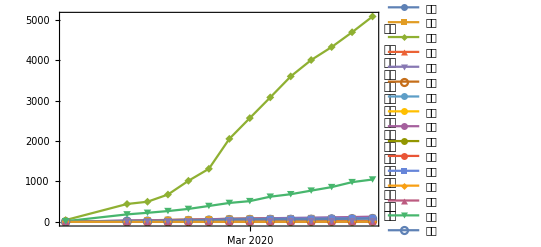

```mathematica
DateListPlot[MapIndexed[Labeled[data[[All,{1,First@#2+1}]],#1]&,$provinces],PlotRange->All,PlotLegends->$provinces,PlotMarkers->Automatic]
```